```mathematica
SetDirectory["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Численные методы\\Wave\\Программа\\wave"];
```

## Тестовая задача 1

```mathematica
data1=Import["test1.txt","Table"];
```

```mathematica
{L1,T1} = First[data1];
```

```mathematica
data1 = Delete[data1,1];
```

```mathematica
n1 = Length[data1[[1]]];
```

```mathematica
m1 = Length[data1];
```

### Точное решение

```mathematica
uExact1[x_,t_]:=Sin[π x]Cos[π t];
```

### Численное решение

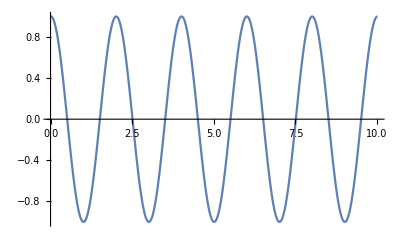

```mathematica
ListLinePlot[Table[{T1/(m1-1)*j,data1[[j]][[Round[n1/2]]]},{j,1,m1}]]
```

```mathematica
Show[ListLinePlot[Table[{T1/(m1-1)*j,data1[[j]][[Round[n1/2]]]},{j,1,m1}]],Plot[uExact1[L1/2,t],{t,0,T1},PlotStyle->Red]];
```

### График погрешности

```mathematica
pogr1={};
```

```mathematica
For[j=0,j<=m1-1,j++,
pogr1 = AppendTo[pogr1,Max[ Table[Abs[data1[[j+1]][[i+1]]-uExact1[L1/(n1-1)*i,T1/(m1-1)*j]],{i,0,n1-1}]]]]
```

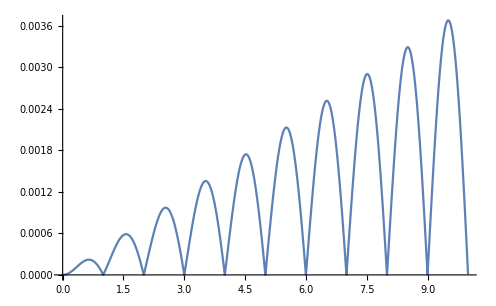

```mathematica
ListLinePlot[Table[{T1/(m1-1)*j,pogr1[[j+1]]},{j,0,m1-1}]]
```

## Тестовая задача 2

```mathematica
data2=Import["test2.txt","Table"];
{L2,T2} = First[data2];
data2=Delete[data2,1];
n2 = Length[data2[[1]]];
m2=Length[data2];
```

```mathematica
ListPlot3D[data2,PlotRange->All]
```

-Graphics3D-

### Точное решение

```mathematica
k=10;
uExact2[x_,t_]:=8/π^3∑_(n=0)^k (1/(2n+1)^3 Sin[(2n+1)π x]Cos[(2n+1)π t])
Plot3D[uExact2[x,t],{x,0,1},{t,0,3}];
```

### Численное решение

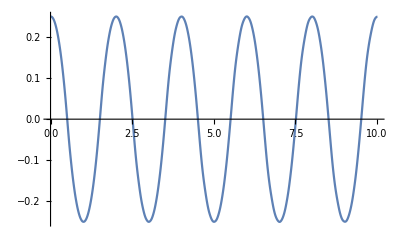

```mathematica
ListLinePlot[Table[{T2/(m2-1)*j,data2[[j]][[Round[n2/2]]]},{j,1,m2}]]
```

### График погрешности

```mathematica
pogr2={};
```

```mathematica
For[j=0,j<=m2-1,j++,
pogr2 = AppendTo[pogr2,Max[ Table[Abs[data2[[j+1]][[i+1]]-uExact2[L2/(n2-1)*i,T2/(m2-1)*j]],{i,0,n2-1}]]]]
```

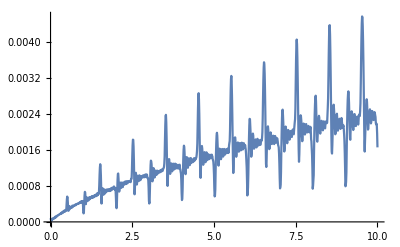

```mathematica
ListLinePlot[Table[{T2/(m2-1)*j,pogr2[[j+1]]},{j,0,m2-1}]]
```

## Тестовая задача 3

```mathematica
dataA3=Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Численные методы\\Wave\\Программа\\wave\\task1_analytical.txt","Table"];
dataN3=Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Численные методы\\Wave\\Программа\\wave\\task1_numerical.txt","Table"];
{L3,T3} = First[dataA3];
dataA3=Delete[dataA3,1];
dataN3=Delete[dataN3,1];
n3 = Length[dataA3[[1]]];
m3=Length[dataA3];
a = -2;
b = 2;
ListPlot3D[{dataA3,dataN3},PlotRange->All]
```

-Graphics3D-

### Численное решение ( в момент времени)

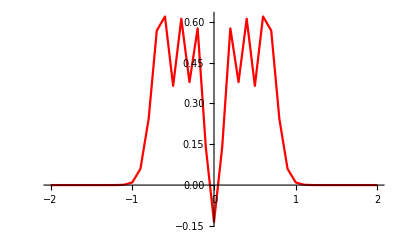

```mathematica
t = Round[m3/2];
ListLinePlot[Table[{a +i*L3/(n3-1),dataA3[[t,i+1]]},{i,0,n3-1}],PlotStyle->Red]
```

```mathematica
Manipulate[Show[ListLinePlot[Table[{a+i*L3/(n3-1),dataA3[[j,i+1]]},{i,0,n3-1}],PlotStyle->Red,PlotRange->All],ListLinePlot[Table[{a+i*L3/(n3-1),dataN3[[j,i+1]]},{i,0,n3-1}],PlotStyle->Blue,PlotRange->All]],{j,1,m3,1}]
```

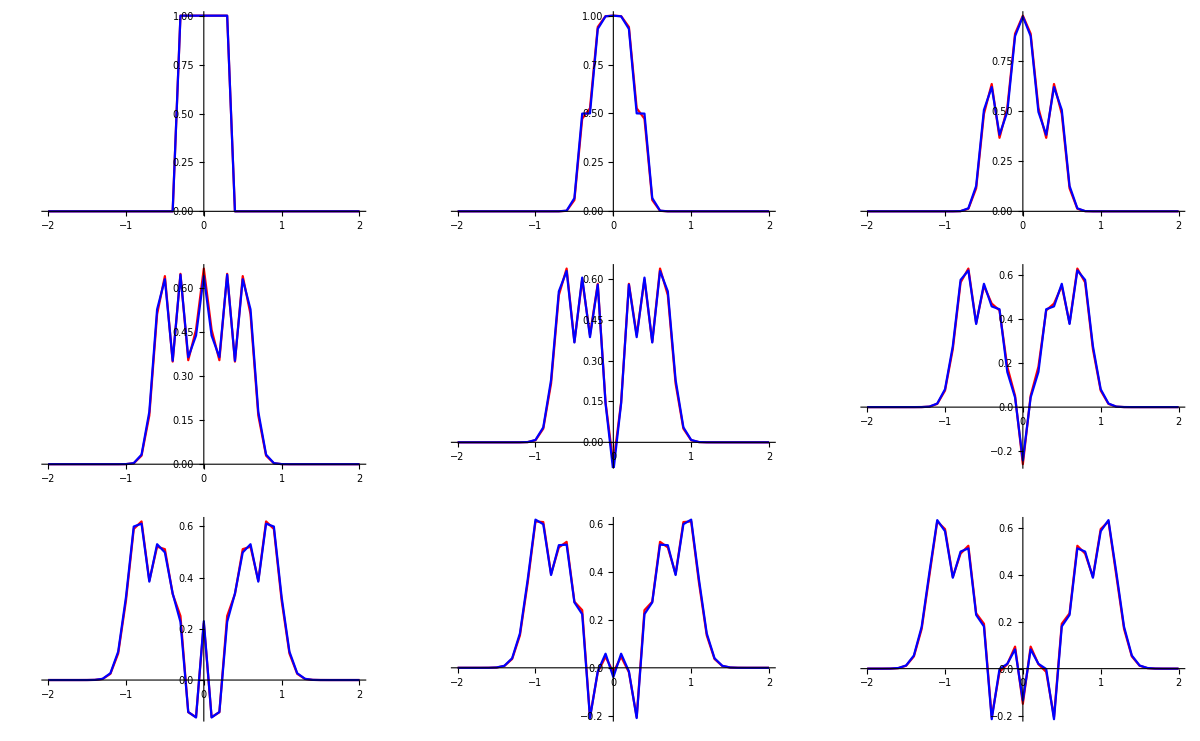

```mathematica
GraphicsGrid@Partition[Table[Show[ListLinePlot[Table[{a +i*L3/(n3-1),dataA3[[j,i+1]]},{i,0,n3-1}],PlotStyle->Red,PlotRange->Full],ListLinePlot[Table[{a +i*L3/(n3-1),dataN3[[j,i+1]]},{i,0,n3-1}],PlotStyle->Blue,PlotRange->Full]]
,{j,1,m3,12}],UpTo[3]]
```

### Численное решение ( в серединной точке)

```mathematica
h = Round[n3/2];
```

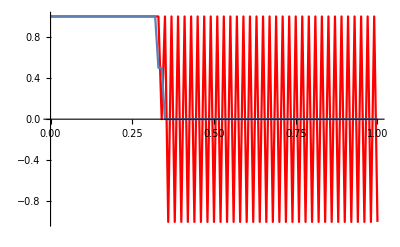

```mathematica
A3 = ListLinePlot[Table[{T3/(m3-1)*j,dataA3[[j+1,h]]},{j,0,m3-1}],PlotStyle->Red];
N3=ListLinePlot[Table[{T3/(m3-1)*j,dataN3[[j+1,h]]},{j,0,m3-1}]];
Show[A3,N3]
```

## Тестовая задача 4

```mathematica
data4=Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Численные методы\\Wave\\Программа\\wave\\task2.txt","Table"];
{L4,T4} = First[data4];
data4=Delete[data4,1];
n4 = Length[data4[[1]]];
m4=Length[data4];
a = -1;
b = 1;
ListPlot3D[data4,PlotRange->All];
```

### Численное решение ( в момент времени)

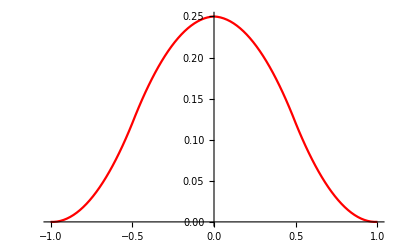

```mathematica
t = Round[m4/2];
ListLinePlot[Table[{a +i*L4/(n4-1),data4[[t,i+1]]},{i,0,n4-1}],PlotStyle->Red]
```

```mathematica
Manipulate[ListLinePlot[Table[{a +i*L4/(n4-1),data4[[j,i+1]]},{i,0,n4-1}],PlotStyle->Red],{j,1,m4,1}]
```

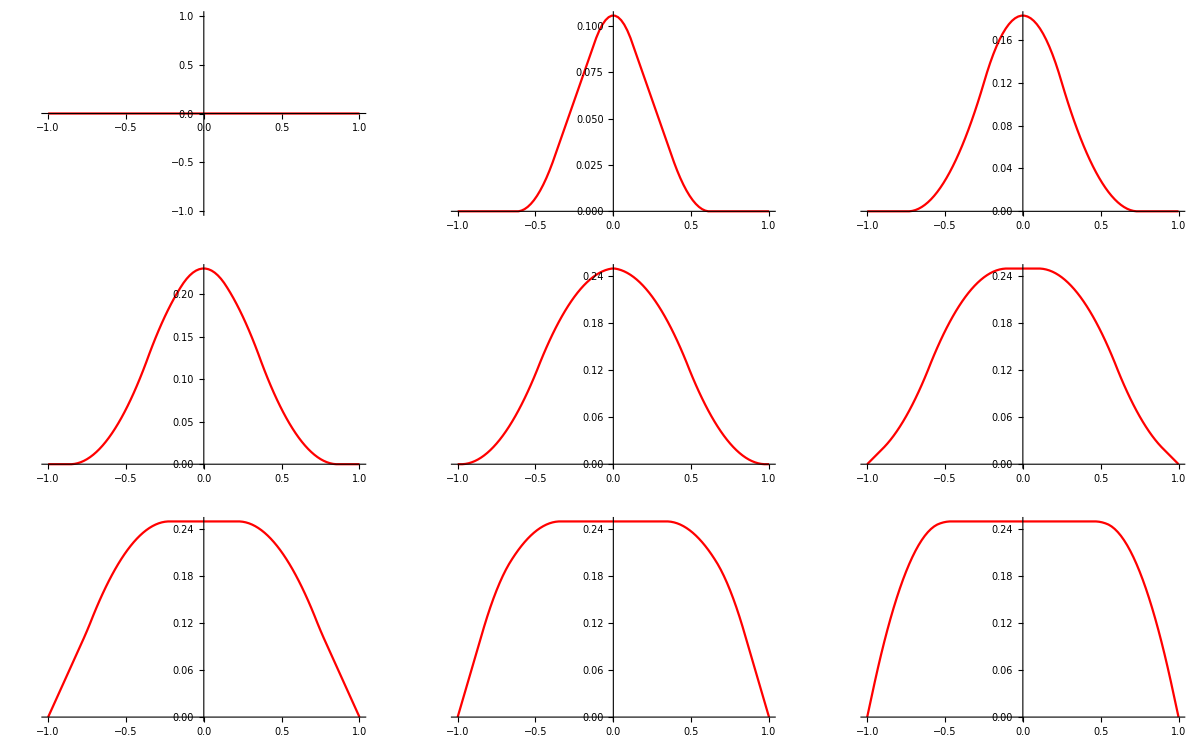

```mathematica
GraphicsGrid@Partition[Table[ListLinePlot[Table[{a +i*L4/(n4-1),data4[[j,i+1]]},{i,0,n4-1}],PlotStyle->Red,PlotRange->Full],{j,1,m4,12}],UpTo[3]]
```

### Численное решение ( в серединной точке)

```mathematica
h = Round[n4/2];
```

```mathematica
ListLinePlot[Table[{T4/(m4-1)*j,data4[[j+1,h]]},{j,0,m4-1}],PlotStyle->Red];
```

## Тестовая задача 5

```mathematica
data5=Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Численные методы\\Wave\\Программа\\wave\\task3.txt","Table"];
{L5,T5} = First[data5];
data5=Delete[data5,1];
n5 = Length[data5[[1]]];
m5=Length[data5];
a = 0;
b = 4π;
ListPlot3D[data5,PlotRange->All]
```

-Graphics3D-

### Численное решение ( в момент времени)

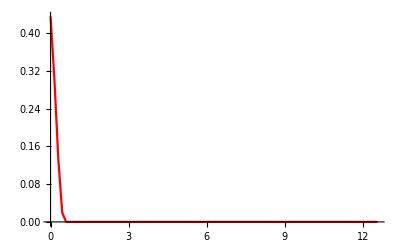

```mathematica
t = Round[m5/2];
ListLinePlot[Table[{a +i*L5/(n5-1),data5[[t,i+1]]},{i,0,n5-1}],PlotStyle->Red]
```

```mathematica
Manipulate[ListLinePlot[Table[{a +i*L5/(n5-1),data5[[j,i+1]]},{i,0,n5-1}],PlotStyle->Red],{j,1,m5,1}]
```

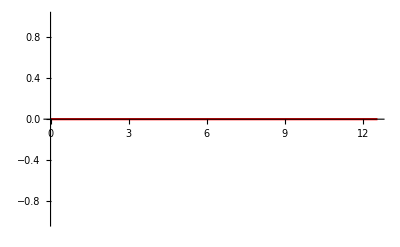

```mathematica
GraphicsGrid@Partition[Table[ListLinePlot[Table[{a +i*L5/(n5-1),data5[[j,i+1]]},{i,0,n5-1}],PlotStyle->Red,PlotRange->Full],{j,1,m5,12}],UpTo[3]]
```

### Численное решение ( в серединной точке)

```mathematica
h = Round[n5/2];
```

```mathematica
ListLinePlot[Table[{T5/(m5-1)*j,data5[[j+1,h]]},{j,0,m5-1}],PlotStyle->Red];
```